## KG

```mathematica
lhs=1/r^2((((r^2+ a^2 rg^2)^2)/(r^2-2rg r + a^2 rg^2)-a^2 rg^2 Sin[θ]^2)Φ[r]S[θ]D[Exp[-I ω t]Exp[I m ϕ],{t,2}] + (4 m a rg r)/(r^2-2rg r + a^2 rg^2)Φ[r]S[θ]D[D[Exp[-I ω t]Exp[I m ϕ],ϕ],t
]+((a^2 rg^2)/(r^2-2rg r + a^2 rg^2)-1/Sin[θ]^2)Φ[r]S[θ]Exp[-I ω t]D[Exp[I m ϕ],{ϕ,2}] -Exp[-I ω t]Exp[I m ϕ]S[θ]D[(r^2-2rg r + a^2 rg^2)D[Φ[r],r],r] - Exp[-I ω t]Exp[I m ϕ]Φ[r] 1/Sin[θ] D[Sin[θ]D[S[θ],θ],θ]+μ^2(r^2+a^2 rg^2 Cos[θ]^2) Exp[-I ω t]Exp[I m ϕ]Φ[r]S[θ]);
```

```mathematica
FullSimplify[lhs]
```

1/r^2 ⅇ^(ⅈ (m ϕ-t ω)) ((4 a m^2 r rg ω S[θ] Φ[r])/(r^2-2 r rg+a^2 rg^2)+μ^2 (r^2+a^2 rg^2 Cos[θ]^2) S[θ] Φ[r]+m^2 (-(a^2 rg^2)/(r^2-2 r rg+a^2 rg^2)+Csc[θ]^2) S[θ] Φ[r]-ω^2 S[θ] (((r^2+a^2 rg^2)^2)/(r^2-2 r rg+a^2 rg^2)-a^2 rg^2 Sin[θ]^2) Φ[r]-Φ[r] (Cot[θ] S'[θ]+S''[θ])-S[θ] (2 (r-rg) Φ'[r]+(r^2-2 r rg+a^2 rg^2) Φ''[r]))

```mathematica
FullSimplify[Series[lhs,{rg,0,1}]]
```

-1/r^2 ⅇ^(ⅈ (m ϕ-t ω)) (Φ[r] (Cot[θ] S'[θ]+S''[θ])+S[θ] (-((r^2 (μ-ω) (μ+ω)+m^2 Csc[θ]^2) Φ[r])+r (2 Φ'[r]+r Φ''[r])))+(2 ⅇ^(ⅈ (m ϕ-t ω)) S[θ] (ω (2 a m^2-r^2 ω) Φ[r]+r (Φ'[r]+r Φ''[r])) rg)/r^3+O[rg]^2

```mathematica
FullSimplify[lhs/.{m->0}]
```

1/r^2 ⅇ^(-ⅈ t ω) (-Φ[r] (Cot[θ] S'[θ]+S''[θ])+S[θ] ((r^2 μ^2-((r^2+a^2 rg^2)^2 ω^2)/(r^2-2 r rg+a^2 rg^2)+a^2 rg^2 (μ^2 Cos[θ]^2+ω^2 Sin[θ]^2)) Φ[r]+2 (-r+rg) Φ'[r]-(r^2-2 r rg+a^2 rg^2) Φ''[r]))

### BoyerL

```mathematica
gUpμν=1/ρ^2{{ρ^2 + 2 GM r, -2 GM r, 0, 0},{-2 GM r, -Δ, 0, -a},{0,0,-1, 0},{0, -a, 0, -1/Sin[θ]^2}}/.{ρ-> r^2+(GM a)^2 Cos[θ]^2,Δ->r^2- 2 GM r + (GM a)^2};
```

```mathematica
mg=FullSimplify[Det[-gUpμν]^(1/2),r>0&&a>0&&θ>0&&θ<π]
```

√(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2))

```mathematica
indxV = {t, r, θ, ϕ};
```

```mathematica
term=0;
Do[
Do[
term += D[mg gUpμν⟦i,j⟧ D[ϕ[t,r,θ,ϕ],indxV⟦j⟧] ,indxV⟦i⟧],{i,Range[1,4]}]
,{j,Range[1,4]}]
term *= mg;
```

```mathematica
term
```

√(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ((4 a r √((a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)/((r^2+a^2 GM^2 Cos[θ]^2)^8)) ϕ^(0,0,0,1)[t,r,θ,ϕ])/((r^2+a^2 GM^2 Cos[θ]^2)^3)-(a (1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM+4 r^3-GM^2 (-2 GM+2 r) (2 r^2+a^2 GM^2 Cos[θ]^2) Cot[θ]^2+4 GM^2 r (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (3 a^2 GM^2 r^2-4 GM r^3+5 r^4-4 GM r (-1+r^2)) Csc[θ]^2-(r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)-1/((r^2+a^2 GM^2 Cos[θ]^2)^9)16 r (a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(0,0,0,1)[t,r,θ,ϕ])/(2 (r^2+a^2 GM^2 Cos[θ]^2)^2 √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)))-1/((r^2+a^2 GM^2 Cos[θ]^2)^2)Csc[θ]^2 √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(0,0,0,2)[t,r,θ,ϕ]-1/((r^2+a^2 GM^2 Cos[θ]^2)^3)4 a^2 GM^2 Cos[θ] √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) Sin[θ] ϕ^(0,0,1,0)[t,r,θ,ϕ]-((1/((r^2+a^2 GM^2 Cos[θ]^2)^9)16 a^2 GM^2 Cos[θ] (a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2) Sin[θ]+1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(2 r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Cot[θ] Csc[θ]^2+a^2 (-2 a^2 GM^4 Cos[θ] (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2) Sin[θ]+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (2 (a^2 GM^2+r (-2 GM+r)) Cot[θ] Csc[θ]^2-2 a^2 Cos[θ] Sin[θ])))) ϕ^(0,0,1,0)[t,r,θ,ϕ])/(2 (r^2+a^2 GM^2 Cos[θ]^2)^2 √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)))-(√((a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)/((r^2+a^2 GM^2 Cos[θ]^2)^8)) ϕ^(0,0,2,0)[t,r,θ,ϕ])/((r^2+a^2 GM^2 Cos[θ]^2)^2)+1/((r^2+a^2 GM^2 Cos[θ]^2)^3)4 r (a^2 GM^2-2 GM r+r^2) √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(0,1,0,0)[t,r,θ,ϕ]-1/((r^2+a^2 GM^2 Cos[θ]^2)^2)(-2 GM+2 r) √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(0,1,0,0)[t,r,θ,ϕ]-((a^2 GM^2-2 GM r+r^2) (1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM+4 r^3-GM^2 (-2 GM+2 r) (2 r^2+a^2 GM^2 Cos[θ]^2) Cot[θ]^2+4 GM^2 r (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (3 a^2 GM^2 r^2-4 GM r^3+5 r^4-4 GM r (-1+r^2)) Csc[θ]^2-(r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)-1/((r^2+a^2 GM^2 Cos[θ]^2)^9)16 r (a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(0,1,0,0)[t,r,θ,ϕ])/(2 (r^2+a^2 GM^2 Cos[θ]^2)^2 √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)))-(2 a √((a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)/((r^2+a^2 GM^2 Cos[θ]^2)^8)) ϕ^(0,1,0,1)[t,r,θ,ϕ])/((r^2+a^2 GM^2 Cos[θ]^2)^2)-1/((r^2+a^2 GM^2 Cos[θ]^2)^2)(a^2 GM^2-2 GM r+r^2) √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(0,2,0,0)[t,r,θ,ϕ]+1/((r^2+a^2 GM^2 Cos[θ]^2)^3)8 GM r^2 √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(1,0,0,0)[t,r,θ,ϕ]-(2 GM √((a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)/((r^2+a^2 GM^2 Cos[θ]^2)^8)) ϕ^(1,0,0,0)[t,r,θ,ϕ])/((r^2+a^2 GM^2 Cos[θ]^2)^2)-(GM r (1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM+4 r^3-GM^2 (-2 GM+2 r) (2 r^2+a^2 GM^2 Cos[θ]^2) Cot[θ]^2+4 GM^2 r (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (3 a^2 GM^2 r^2-4 GM r^3+5 r^4-4 GM r (-1+r^2)) Csc[θ]^2-(r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)-1/((r^2+a^2 GM^2 Cos[θ]^2)^9)16 r (a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(1,0,0,0)[t,r,θ,ϕ])/((r^2+a^2 GM^2 Cos[θ]^2)^2 √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)))-1/((r^2+a^2 GM^2 Cos[θ]^2)^2)4 GM r √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(1,1,0,0)[t,r,θ,ϕ]+1/((r^2+a^2 GM^2 Cos[θ]^2)^2)(2 GM r+(r^2+a^2 GM^2 Cos[θ]^2)^2) √(1/((r^2+a^2 GM^2 Cos[θ]^2)^8)(a^2 (2 GM r+r^4+GM^2 (2 r^2+a^2 GM^2 Cos[θ]^2) (a^2 Cos[θ]^2-(a^2 GM^2+r (-2 GM+r)) Cot[θ]^2))-r (r^5-2 GM r^2 (-1+r^2)+a^2 GM^2 (2 GM+r^3)) Csc[θ]^2)) ϕ^(2,0,0,0)[t,r,θ,ϕ])

## Radial [far]

```mathematica
lhs=1/r^2(D[(r^2-2GM r + a^2 GM^2)D[R[r],r],r]+((ω^2(r^2+a^2 GM^2)^2 - 4 GM^2 a m ω r + m^2 GM^2 a^2)/(r^2-2GM r + a^2 GM^2)-(ω^2 GM^2 a^2+μ^2 r^2 + l (l+1)))R[r])
```

1/r^2((-l (1+l)-r^2 μ^2-a^2 GM^2 ω^2+(a^2 GM^2 m^2-4 a GM^2 m r ω+(a^2 GM^2+r^2)^2 ω^2)/(a^2 GM^2-2 GM r+r^2)) R[r]+(-2 GM+2 r) R'[r]+(a^2 GM^2-2 GM r+r^2) R''[r])

```mathematica
Expand[-FullSimplify[Normal[FullSimplify[Series[lhs,{GM,0,1}]]]]]
```

(l R[r])/r^2+(l^2 R[r])/r^2+μ^2 R[r]-ω^2 R[r]-(2 GM ω^2 R[r])/r+(2 GM R'[r])/r^2-(2 R'[r])/r-R''[r]+(2 GM R''[r])/r

```mathematica
FullSimplify[D[Exp[-r/r0](2 r/r0)^l,r] 1/(Exp[-r/r0](2 r/r0)^l)]/.{r0-> 1/(GM μ^2)}
```

l/r-GM μ^2

```mathematica
FullSimplify[D[Exp[-r/r0](2 r/r0)^l,{r,2}] 1/(Exp[-r/r0](2 r/r0)^l)]/.{r0-> 1/(GM μ^2)}
```

((-1+l) l)/r^2-(2 GM l μ^2)/r+GM^2 μ^4

```mathematica
-(2 GM ω^2 R[r])/r
```

```mathematica
Series[(2 GM R'[r])/r^2+(2 GM R''[r])/r/.{R'[r]-> R[r](l/r-GM μ^2),R''[r]-> R[r](((-1+l) l)/r^2-(2 GM l μ^2)/r+GM^2 μ^4) },{r,Infinity,1}]
```

R[r] O[1/r]^2+R[r] ((2 GM^3 μ^4)/r+O[1/r]^2)

## Radial [near]

```mathematica
lhs=1/r^2(D[(r^2-2GM r + a^2 GM^2)D[R[r],r],r]+((ω^2(r^2+a^2 GM^2)^2 - 4 GM^2 a m ω r + m^2 GM^2 a^2)/(r^2-2GM r + a^2 GM^2)-(ω^2 GM^2 a^2+μ^2 r^2 + l (l+1)))R[r]);
```

```mathematica
Solve[z== (r μ - α rp)/(α rp - α rm),r]
```

{{r→((rp-rm z+rp z) α)/μ}}

```mathematica
rr[z_]:=(rp α + z α (rp - rm))/μ;
```

```mathematica
Normal[Series[FullSimplify[1/rr[z]^2 D[(rr[z]^2-2GM rr[z] + a^2 GM^2)D[R[z],z],z]],{z,0,0}]]
```

(2 (rm-rp) α (-rp α+GM μ) R'[0]+(rp^2 α^2-2 GM rp α μ+a^2 GM^2 μ^2) R''[0])/(rp^2 α^2)

```mathematica
dt=FullSimplify[Normal[Series[FullSimplify[D[(rr[z]^2-2GM rr[z] + a^2 GM^2)D[R[z],z],z]],{z,0,1}]]/.{ GM-> α/μ,rp-> 1+√(1-a^2),rm-> 1-√(1-a^2)},a>0&&a<1]
```

-(4 (-1+a^2) α^2 ((1+2 z) R'[0]+2 z R''[0]))/μ^2

```mathematica
st=Normal[FullSimplify[Series[((ω^2(rr[z]^2+a^2 GM^2)^2 - 4 GM^2 a m ω rr[z] + m^2 GM^2 a^2)/(rr[z]^2-2GM rr[z] + a^2 GM^2)-(ω^2 GM^2 a^2+μ^2 rr[z]^2 + l (l+1)))R[z]/.{rp-> 1+√(1-a^2),rm-> 1-√(1-a^2), GM-> α/μ},{z,0,0}],a>0&&a<1]]
```

((4 a (1+√(1-a^2)) m α μ ω-8 (1+√(1-a^2)) α^2 ω^2+a^2 (-m^2 μ^2+4 α^2 ω^2)) R[0])/(4 (-1+a^2) z μ^2)+1/(4 (-1+a^2) μ^2)(-4 (-1+a^2) l μ^2 R[0]-4 (-1+a^2) l^2 μ^2 R[0]+4 a^4 α^2 (μ-ω) (μ+ω) R[0]+4 a m α μ ω ((-1+√(1-a^2)) R[0]+(1+√(1-a^2)) R'[0])+8 (1+√(1-a^2)) α^2 (μ^2 R[0]-ω^2 (3 R[0]+R'[0]))+a^2 (m^2 μ^2 (R[0]-R'[0])+4 α^2 (-((3+2 √(1-a^2)) μ^2 R[0])+ω^2 (4 (2+√(1-a^2)) R[0]+R'[0]))))

```mathematica
FullSimplify[dt + st/.{rp-> 1+√(1-a^2),rm-> 1-√(1-a^2), GM-> α/μ},a>0&&a<1]
```

FullSimplify::infd: Expression (μ^2 (-l (1+l)-(1+√Plus[«2»])^2 α^2-(a^2 α^2 ω^2)/μ^2+((a^2 m^2 α^2)/μ^2-(4 a (1+Power[«2»]) m α^3 ω)/μ^3+Plus[«2»]^2 ω^2)/(Power[«2»] Power[«2»] Power[«2»]+Plus[«2»] α Plus[«2»] Power[«2»])) R[0])/((1+√(1-Power[«2»]))^2 α^2)+(4 (-1+a^2) ((-1-√Plus[«2»]+2 (-1+Power[«2»]) z) R'[0]-2 (1+√(1+Times[«2»])) z R''[0]))/(1+√(1-Power[«2»]))^3 simplified to ComplexInfinity.

ComplexInfinity

```mathematica
st=Normal[FullSimplify[Series[rr[z]^2-2GM rr[z] + a^2 GM^2/.{rp-> 1+√(1-a^2),rm-> 1-√(1-a^2), GM-> α/μ},{z,0,1}],a>0&&a<1]]
```

-(4 (-1+a^2) z α^2)/μ^2

```mathematica
1/(r-rp)^(I α)D[(r-rp)^(I α),r]
```

(ⅈ α)/(r-rp)

```mathematica
FullSimplify[(1-ω^2/μ^2)+Pp/(r μ - rp μ)^2+Pm/(r μ - rm μ)^2-Ap/((rp μ - rm μ)(r μ - r p))+Am/((rp μ - rm μ)(r μ - r m))/.{Am-> Pp^2+Pm^2+γ2+γp2,Ap-> Pp^2+Pm^2+γ2+γm2}/.{Pp-> α (a m - 2 rp ω)/(rp  μ - rm μ),Pm-> α (a m - 2 rm ω)/(rp μ - rm μ),γ2-> 1/4(rp μ-rm μ)^2(1- ω^2/μ^2),γp2->α^2(1-7 ω^2/μ^2)+α (rp μ - rm μ)(1-2 ω^2/μ^2),γm2->α^2(1-7 ω^2/μ^2)-α (rp μ - rm μ)(1-2 ω^2/μ^2)}]
```

1-ω^2/μ^2+(α (-a m+2 rm ω))/((r-rm)^2 (rm-rp) μ^3)+(α (a m-2 rp ω))/((r-rp)^2 (-rm+rp) μ^3)-(1/4 (rm-rp)^2 (μ-ω) (μ+ω)+((rm-rp) α (μ^2-2 ω^2))/μ+(α^2 (2 a^2 m^2+(rm-rp)^2 μ^2-4 a m (rm+rp) ω+(-3 rm^2+14 rm rp-3 rp^2) ω^2))/((rm-rp)^2 μ^2))/(r (rm-rp) (p-μ) μ)+(1/4 (rm-rp)^2 (μ-ω) (μ+ω)+(α^2 (a m-2 rm ω)^2)/(-rm μ+rp μ)^2+(α^2 (a m-2 rp ω)^2)/(-rm μ+rp μ)^2+α^2 (1-(7 ω^2)/μ^2)+(-rm+rp) α μ (1-(2 ω^2)/μ^2))/(r (rm-rp) (m-μ) μ)

```mathematica
Series[-(-(ω^2(r^2+GM^2 a^2)^2)/((r^2-2GM r + GM^2 a^2)^2) + μ^2 r^2/(r^2-2GM r + GM^2 a^2)),{GM,0,1}]
```

(-μ^2+ω^2)-(2 (μ^2-2 ω^2) GM)/r+O[GM]^2

```mathematica
DSolve[D[y[x],{x,2}]==α^4 y[x],y[x],x]
```

{{y[x]→ⅇ^(x α^2) C[1]+ⅇ^(-x α^2) C[2]}}

```mathematica
Series[α^2-α^2(1-α^2/2)^2,{α,0,4}]
```

α^4+O[α]^5

```mathematica
FullSimplify[D[(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2)),r]]
```

2/(a^2+(-2+r) r)

```mathematica
D[r+Log[a^2-2 r+r^2],r]
```

1+(-2+2 r)/(a^2-2 r+r^2)

```mathematica
a^2-2 r+r^2+-2+2 r
```

-2+a^2+r^2

```mathematica
Integrate[(r^2+a^2)/(r^2-2r +a^2),r]
```

r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2]

```mathematica
r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2] /.{r->1+√(1-a^2)}
```

1+√(1-a^2)+(2 ArcTan[(√(1-a^2))/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 (1+√(1-a^2))+(1+√(1-a^2))^2]

```mathematica
N[Limit[r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2]-+7.2073078414566805 ⅈ,r->1+√(1-a^2)]]
```

-∞

```mathematica
N[Limit[r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2]-+7.2073078414566805 ⅈ,r->Infinity]]
```

∞

```mathematica
1+√(1-a^2)/.{a->0.9}
```

1.43589

```mathematica
√(-1+a^2)/.{a->0.9}
```

0.+0.43589 ⅈ

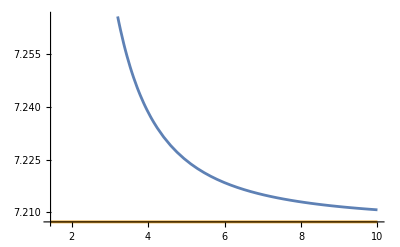

```mathematica
Plot[{Abs[2 ArcTan[(-1+r)/(√(-1+a^2))]/(√(-1+a^2))]/.{a->0.9},Im[2 ArcTan[(-1+r)/(√(-1+a^2))]/(√(-1+a^2))]/.{a->0.9}},{r,1.45,10}]
```

```mathematica
D
```

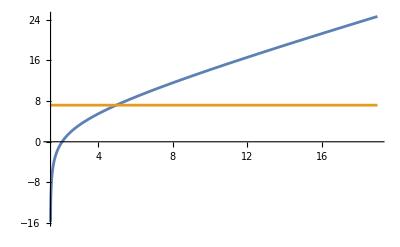

```mathematica
Plot[{Re[r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2]]/.{a->0.9},Im[r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2]]/.{a->0.9}},{r,1.441,19}]
```

```mathematica
FullSimplify[Series[(r^2+rg^2 a^2 Cos[θ]^2)/(r^2-2rg r + rg^2 a^2),{r,rg,0}]]/.{a->.99}
```

-50.2513 (1+0.9801 Cos[θ]^2)+O[r-rg]^1

```mathematica
FullSimplify[Integrate[(r^2+a^2)/(r^2-2GM r + a^2),r],a>0&&a<1&&GM>0&&r>0]
```

r+GM ((2 GM ArcTan[(-GM+r)/(√((a-GM) (a+GM)))])/(√((a-GM) (a+GM)))+Log[a^2-2 GM r+r^2])

```mathematica
FullSimplify[Solve[D[u[r]/(√(r^2+a^2)),{r,2}]+(2 r - 2)/Δ D[u[r]/(√(r^2+a^2)),r]==Ψ u[r]/(√(r^2+a^2))+ρ/Δ Λ,u''[r]],a>0&&r>0]
```

{{u''[r]→1/((a^2+r^2)^2 Δ)((a^2+r^2)^(5/2) Λ ρ+(a^4 Δ Ψ+a^2 (Δ+2 r (-1+r+r Δ Ψ))+r^2 (-2 Δ+r (-2+r (2+Δ Ψ)))) u[r]-2 (a^2+r^2) ((-1+r) (a^2+r^2)-r Δ) u'[r])}}

```mathematica
FullSimplify[Solve[D[ Δ[rp[r]] D[R[rp[r]],r],r]==Ψ,R''[rp[r]]]]
```

{{R''[rp[r]]→(Ψ-R'[rp[r]] (rp'[r]^2 Δ'[rp[r]]+Δ[rp[r]] rp''[r]))/(Δ[rp[r]] rp'[r]^2)}}

```mathematica
Integrate[1/(√(r^2-2r + a^2)),r]
```

-Log[1-r+√(a^2-2 r+r^2)]

```mathematica
N[-299+√(89400+(.1)^2)]
```

-0.00165552

```mathematica
Limit[-Log[1-r+√(a^2-2 r+r^2)],r->300]
```

-Log[-299+√(89400+a^2)]

```mathematica
FullSimplify[D[-Log[1-r+√(a^2-2 r+r^2)],r]]
```

1/(√(a^2+(-2+r) r))

```mathematica
D[Exp[-I (ω + λ δω)t],{t,2}]
```

-ⅇ^(-ⅈ t (δω λ+ω)) (δω λ+ω)^2

```mathematica
Series[(δω λ+ω)^2,{λ,0,1}]
```

ω^2+2 δω ω λ+O[λ]^2

```mathematica
5/2-2
```

1/2

```mathematica
x
```

```mathematica
D[R[r ],{r,2}]+(2 r - 2)/Δ D[R[r ],r]
```

((-2+2 r) R'[r])/Δ+R''[r]

```mathematica
D[R[r],{r,2}]+(2 r - 2)/Δ D[R[r ],r]
```

```mathematica
DSolve[D[y[x],{x,2}]==-β D[y[x],x]/x-α y[x]/x,y[x],x]
```

{{y[x]→x^(1+1/2 (-1+β)-β) α^(1+1/2 (-1+β)-β) BesselJ[1-β,2 √x √α] C[2] Gamma[2-β]+x^((1-β)/2) α^((1-β)/2) BesselJ[-1+β,2 √x √α] C[1] Gamma[β]}}

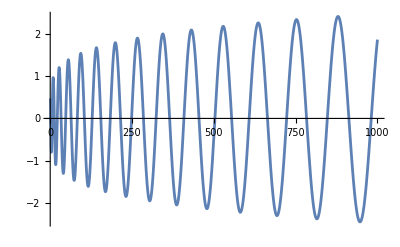

```mathematica
Plot[x^(1+1/2 (-1+β)-β) α^(1+1/2 (-1+β)-β) BesselJ[1-β,2 √x √α] Gamma[2-β]/.{α->2, β->.1},{x,1,1000}]
```

```mathematica
Expand[FullSimplify[D[(r^2-2r + a^2)D[u[r]/((r^2+a^2)^(1/2)),r],r]]]
```

-(a^4 u[r])/((a^2+r^2)^(5/2))+(4 a^2 r u[r])/((a^2+r^2)^(5/2))-(a^2 r^2 u[r])/((a^2+r^2)^(5/2))-(2 r^3 u[r])/((a^2+r^2)^(5/2))-(2 a^4 u'[r])/((a^2+r^2)^(5/2))+(2 r^4 u'[r])/((a^2+r^2)^(5/2))+(a^6 u''[r])/((a^2+r^2)^(5/2))-(2 a^4 r u''[r])/((a^2+r^2)^(5/2))+(3 a^4 r^2 u''[r])/((a^2+r^2)^(5/2))-(4 a^2 r^3 u''[r])/((a^2+r^2)^(5/2))+(3 a^2 r^4 u''[r])/((a^2+r^2)^(5/2))-(2 r^5 u''[r])/((a^2+r^2)^(5/2))+(r^6 u''[r])/((a^2+r^2)^(5/2))

```mathematica
FullSimplify[(a^4 u[r])/((a^2+r^2)^(5/2))+(4 a^2 r u[r])/((a^2+r^2)^(5/2))-(a^2 r^2 u[r])/((a^2+r^2)^(5/2))-(2 r^3 u[r])/((a^2+r^2)^(5/2))]
```

((a^4-a^2 (-4+r) r-2 r^3) u[r])/((a^2+r^2)^(5/2))

```mathematica
FullSimplify[-(2 a^4 u'[r])/((a^2+r^2)^(5/2))+(2 r^4 u'[r])/((a^2+r^2)^(5/2))]
```

(2 (-a^2+r^2) u'[r])/((a^2+r^2)^(3/2))

```mathematica
FullSimplify[(a^6 u''[r])/((a^2+r^2)^(5/2))-(2 a^4 r u''[r])/((a^2+r^2)^(5/2))+(3 a^4 r^2 u''[r])/((a^2+r^2)^(5/2))-(4 a^2 r^3 u''[r])/((a^2+r^2)^(5/2))+(3 a^2 r^4 u''[r])/((a^2+r^2)^(5/2))-(2 r^5 u''[r])/((a^2+r^2)^(5/2))+(r^6 u''[r])/((a^2+r^2)^(5/2))]
```

((a^2+(-2+r) r) u''[r])/(√(a^2+r^2))

```mathematica
FullSimplify[Solve[-2 ((1+2 n (-2+r)-r) r^2+a^2 (1-r+2 n r))==0,n]]
```

{{n→((-1+r) (a^2+r^2))/(2 r (a^2+(-2+r) r))}}

```mathematica
Limit[((-1+r) (a^2+r^2))/(2 r (a^2+(-2+r) r)),r->Infinity]
```

1/2

```mathematica
FullSimplify[(r[rs]^2+a^2)/Δ D[Δ (r[rs]^2+a^2)/Δ D[u[rs]/(√(r[rs]^2+a^2)),rs],rs]+u[rs]/(√(r[rs]^2+a^2))((ω(r^2+a^2))^2+Δ(-μ^2(r^2+a^2)+a^2(μ^2-ω^2)))/Δ/.{ r''[rs]->-(2 r[rs] (a^2-2 r[rs]+r[rs]^2) r'[rs])/((a^2+r[rs]^2)^2)+(-2 r'[rs]+2 r[rs] r'[rs])/(a^2+r[rs]^2)}/.{r'[rs]->Δ/(r^2+a^2)}/.{r[rs]->r}]
```

((Δ (2 a^2 r-2 r^3-a^2 Δ-r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs]+(a^2+r^2)^4 u''[rs])/((a^2+r^2)^(5/2) Δ)

```mathematica
Expand[Solve[((Δ (2 a^2 r-2 r^3-a^2 Δ-r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs]+(a^2+r^2)^4 u''[rs])/((a^2+r^2)^(5/2) Δ)==T,u''[rs]]]
```

{{u''[rs]→(T Δ)/((a^2+r^2)^(3/2))-(2 a^2 r Δ u[rs])/((a^2+r^2)^4)+(2 r^3 Δ u[rs])/((a^2+r^2)^4)+(a^2 Δ^2 u[rs])/((a^2+r^2)^4)+(a^4 r^2 Δ μ^2 u[rs])/((a^2+r^2)^4)+(2 a^2 r^4 Δ μ^2 u[rs])/((a^2+r^2)^4)+(r^6 Δ μ^2 u[rs])/((a^2+r^2)^4)-(a^8 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^6 r^2 ω^2 u[rs])/((a^2+r^2)^4)-(6 a^4 r^4 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^2 r^6 ω^2 u[rs])/((a^2+r^2)^4)-(r^8 ω^2 u[rs])/((a^2+r^2)^4)+(a^6 Δ ω^2 u[rs])/((a^2+r^2)^4)+(2 a^4 r^2 Δ ω^2 u[rs])/((a^2+r^2)^4)+(a^2 r^4 Δ ω^2 u[rs])/((a^2+r^2)^4)}}

```mathematica
FullSimplify[-(2 a^2 r Δ u[rs])/((a^2+r^2)^4)+(2 r^3 Δ u[rs])/((a^2+r^2)^4)+(a^2 Δ^2 u[rs])/((a^2+r^2)^4)+(a^4 r^2 Δ μ^2 u[rs])/((a^2+r^2)^4)+(2 a^2 r^4 Δ μ^2 u[rs])/((a^2+r^2)^4)+(r^6 Δ μ^2 u[rs])/((a^2+r^2)^4)-(a^8 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^6 r^2 ω^2 u[rs])/((a^2+r^2)^4)-(6 a^4 r^4 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^2 r^6 ω^2 u[rs])/((a^2+r^2)^4)-(r^8 ω^2 u[rs])/((a^2+r^2)^4)+(a^6 Δ ω^2 u[rs])/((a^2+r^2)^4)+(2 a^4 r^2 Δ ω^2 u[rs])/((a^2+r^2)^4)+(a^2 r^4 Δ ω^2 u[rs])/((a^2+r^2)^4)]
```

((Δ (-2 a^2 r+2 r^3+a^2 Δ+r^2 (a^2+r^2)^2 μ^2)-(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs])/((a^2+r^2)^4)

```mathematica
n0 Exp[-t1 Γ]
```

```mathematica
FullSimplify[(r[rs]^2+a^2)/Δ D[Δ (r[rs]^2+a^2)/Δ D[u[rs]/(√(r[rs]^2+a^2)),rs],rs]+1/Δ u[rs]/(√(r[rs]^2+a^2))((r^2+a^2)^2 ω^2+μ^2 r^2 Δ - ω^2 a^2 Δ)/.{ r''[rs]->-(2 r[rs] (a^2-2 r[rs]+r[rs]^2) r'[rs])/((a^2+r[rs]^2)^2)+(-2 r'[rs]+2 r[rs] r'[rs])/(a^2+r[rs]^2)}/.{r'[rs]->Δ/(r^2+a^2)}/.{r[rs]->r}]
```

((Δ (2 a^2 r-2 r^3-a^2 Δ+r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs]+(a^2+r^2)^4 u''[rs])/((a^2+r^2)^(5/2) Δ)

```mathematica
Expand[Solve[((Δ (2 a^2 r-2 r^3-a^2 Δ+r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs]+(a^2+r^2)^4 u''[rs])/((a^2+r^2)^(5/2) Δ)==T,u''[rs]]]
```

{{u''[rs]→(T Δ)/((a^2+r^2)^(3/2))-(2 a^2 r Δ u[rs])/((a^2+r^2)^4)+(2 r^3 Δ u[rs])/((a^2+r^2)^4)+(a^2 Δ^2 u[rs])/((a^2+r^2)^4)-(a^4 r^2 Δ μ^2 u[rs])/((a^2+r^2)^4)-(2 a^2 r^4 Δ μ^2 u[rs])/((a^2+r^2)^4)-(r^6 Δ μ^2 u[rs])/((a^2+r^2)^4)-(a^8 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^6 r^2 ω^2 u[rs])/((a^2+r^2)^4)-(6 a^4 r^4 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^2 r^6 ω^2 u[rs])/((a^2+r^2)^4)-(r^8 ω^2 u[rs])/((a^2+r^2)^4)+(a^6 Δ ω^2 u[rs])/((a^2+r^2)^4)+(2 a^4 r^2 Δ ω^2 u[rs])/((a^2+r^2)^4)+(a^2 r^4 Δ ω^2 u[rs])/((a^2+r^2)^4)}}

```mathematica
FullSimplify[-(2 a^2 r Δ u[rs])/((a^2+r^2)^4)+(2 r^3 Δ u[rs])/((a^2+r^2)^4)+(a^2 Δ^2 u[rs])/((a^2+r^2)^4)-(a^4 r^2 Δ μ^2 u[rs])/((a^2+r^2)^4)-(2 a^2 r^4 Δ μ^2 u[rs])/((a^2+r^2)^4)-(r^6 Δ μ^2 u[rs])/((a^2+r^2)^4)-(a^8 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^6 r^2 ω^2 u[rs])/((a^2+r^2)^4)-(6 a^4 r^4 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^2 r^6 ω^2 u[rs])/((a^2+r^2)^4)-(r^8 ω^2 u[rs])/((a^2+r^2)^4)+(a^6 Δ ω^2 u[rs])/((a^2+r^2)^4)+(2 a^4 r^2 Δ ω^2 u[rs])/((a^2+r^2)^4)+(a^2 r^4 Δ ω^2 u[rs])/((a^2+r^2)^4)]
```

-((Δ (2 a^2 r-2 r^3-a^2 Δ+r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs])/((a^2+r^2)^4)

```mathematica
FullSimplify[((Δ (-2 a^2 r+2 r^3+a^2 Δ+r^2 (a^2+r^2)^2 μ^2)-(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs])/((a^2+r^2)^4)-(-((Δ (2 a^2 r-2 r^3-a^2 Δ+r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs])/((a^2+r^2)^4))]
```

(2 r^2 Δ μ^2 u[rs])/((a^2+r^2)^2)

```mathematica
Series[((Δ (-2 a^2 r+2 r^3+a^2 Δ+r^2 (a^2+r^2)^2 μ^2)-(a^2+r^2)^2 ((a^2+r^2)^2-a^2 Δ) ω^2) u[rs])/((a^2+r^2)^4)/.{Δ->r^2-2r +a^2},{r,Infinity,1}]
```

(μ^2-ω^2) u[rs]-(2 (μ^2 u[rs]))/r+O[1/r]^2

```mathematica
D[r + 2 Log[r/2-1],r]
```

1+1/(-1+r/2)

```mathematica
√((μ α GM)^3/(GM)^3)
```

```mathematica
N[(3 3 - 3/2-1)2]
```

13.

```mathematica
2^7
```

128

```mathematica
DSolve[{D[y[x],{x,2}]==(α^2 y[x])/x+d[x]},y[x],x]
```

{{y[x]→-√x α BesselI[1,2 √x α] C[1]+2 √x α BesselK[1,2 √x α] C[2]-√x α BesselI[1,2 √x α] -(2 BesselK[1,2 α √K[1]] d[K[1]] √K[1])/αK[1]1x+2 √x α BesselK[1,2 √x α] -(BesselI[1,2 α √K[2]] d[K[2]] √K[2])/αK[2]1x}}

```mathematica
Integrate[(r^2+a^2)/(r^2-2r +a^2),r]
```

r+(2 ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))+Log[a^2-2 r+r^2]

```mathematica
DSolve[D[y[x],{x,2}]==α^n f[x]/x,y[x],x]
```

{{y[x]→C[1]+x C[2]+(α^n f[K[1]])/K[1]K[1]1K[2]K[2]1x}}

```mathematica
FullSimplify[D[r+2 rp/(rp-rm)Log[r/rp-1]-2 rm/(rp-rm)Log[r/rm-1]/.{rp->1 + √(1-a^2),rm-> 1- √(1-a^2)},r]]
```

1+(2 r)/(a^2+(-2+r) r)

```mathematica
Series[(T Δ)/((a^2+r^2)^(3/2))-(2 a^2 r Δ u[rs])/((a^2+r^2)^4)+(2 r^3 Δ u[rs])/((a^2+r^2)^4)+(a^2 Δ^2 u[rs])/((a^2+r^2)^4)+(a^4 r^2 Δ μ^2 u[rs])/((a^2+r^2)^4)+(2 a^2 r^4 Δ μ^2 u[rs])/((a^2+r^2)^4)+(r^6 Δ μ^2 u[rs])/((a^2+r^2)^4)-(a^8 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^6 r^2 ω^2 u[rs])/((a^2+r^2)^4)-(6 a^4 r^4 ω^2 u[rs])/((a^2+r^2)^4)-(4 a^2 r^6 ω^2 u[rs])/((a^2+r^2)^4)-(r^8 ω^2 u[rs])/((a^2+r^2)^4)+(a^6 Δ ω^2 u[rs])/((a^2+r^2)^4)+(2 a^4 r^2 Δ ω^2 u[rs])/((a^2+r^2)^4)+(a^2 r^4 Δ ω^2 u[rs])/((a^2+r^2)^4)/.{Δ-> r^2-2r + a^2},{r,Infinity,1}]
```

(μ^2 u[rs]-ω^2 u[rs])+(T-2 μ^2 u[rs])/r+O[1/r]^2

```mathematica
Series[ω^2-μ^2(r^2-2r+a^2)/(r^2+a^2)+(r^2-2r+a^2)/((r^2+a^2)^2)λ,{r,Infinity,2}]
```

(-μ^2+ω^2)+(2 μ^2)/r+λ/r^2+O[1/r]^3

```mathematica
6/0.02
```

300.

## Clean

```mathematica
out1=FullSimplify[(Δ/(r[rs]^2+a^2))^-1 D[Δ (Δ/(r[rs]^2+a^2))^-1 D[u[rs]/(√(r[rs]^2+a^2)),rs],rs]-((r^2+a^2)^2(-I ω)^2)/Δ(u[rs]/(√(r[rs]^2+a^2)))+μ^2 r^2(u[rs]/(√(r[rs]^2+a^2)))-ρ^2 S];
outsimp =FullSimplify[ out1/.{ r''[rs]->-(2 r[rs] (a^2-2 r[rs]+r[rs]^2) r'[rs])/((a^2+r[rs]^2)^2)+(-2 r'[rs]+2 r[rs] r'[rs])/(a^2+r[rs]^2)}/.{r'[rs]->Δ/(r^2+a^2)}/.{r[rs]->r}]
```

-S ρ^2+((Δ (2 a^2 r-2 r^3-a^2 Δ+r^2 (a^2+r^2)^2 μ^2)+(a^2+r^2)^4 ω^2) u[rs]+(a^2+r^2)^4 u''[rs])/((a^2+r^2)^(5/2) Δ)

```mathematica
FullSimplify[Solve[outsimp==0,u''[rs]]]
```

{{u''[rs]→(S Δ ρ^2)/((a^2+r^2)^(3/2))+((Δ (-2 a^2 r+2 r^3+a^2 Δ-r^2 (a^2+r^2)^2 μ^2))/((a^2+r^2)^4)-ω^2) u[rs]}}

```mathematica
Series[(S Δ ρ^2)/((a^2+r^2)^(3/2))+((Δ (-2 a^2 r+2 r^3+a^2 Δ+r^2 (a^2+r^2)^2 α^2))/((a^2+r^2)^4)-(α(1-α^2))^2) u[rs]/.{Δ->r^2-2r + a^2},{α,Infinity,0},{r,a,1}]
```

-u[rs] α^6+2 u[rs] α^4+(-((1+a) u[rs])/(2 a)+((-1+a) u[rs] (r-a))/(2 a^2)+O[r-a]^2) α^2+((((-a+a^2) S ρ^2)/(√2 (a^2)^(3/2))+((-1+a)^2 u[rs])/(4 a^4))+(-((-1+a) S ρ^2)/(2 √2 (a^2)^(3/2))-((-2+a) (-1+a) u[rs])/(2 a^5)) (r-a)+O[r-a]^2)+O[1/α]^1

```mathematica
1/r^2(r^2/(r[rs]^2+a^2))^-1 D[r^2(r^2/(r[rs]^2+a^2))^-1 D[u[rs]/(√(r[rs]^2+a^2)),rs],rs]/.{r[rs]->r}/.{r'[rs]->1}
```

((a^2+r^2) (2 r (-(r u[rs])/((a^2+r^2)^(3/2))+u'[rs]/(√(a^2+r^2)))+(a^2+r^2) ((3 r^2 u[rs])/((a^2+r^2)^(5/2))-u[rs]/((a^2+r^2)^(3/2))-(2 r u'[rs])/((a^2+r^2)^(3/2))-(r u[rs] r''[rs])/((a^2+r^2)^(3/2))+u''[rs]/(√(a^2+r^2)))))/r^4

```mathematica
1/r^2 D[r^2 D[ϕ[r],r],r]
```

(2 r ϕ'[r]+r^2 ϕ''[r])/r^2

```mathematica
FullSimplify[SphericalHarmonicY[1,1,θ,ϕ]^2 Conjugate[SphericalHarmonicY[2,2,θ,ϕ]]Conjugate[SphericalHarmonicY[0,0,θ,ϕ]],ϕ∈Reals&&θ∈Reals]
```

(3 √(15/2) Sin[θ]^4)/(64 π^2)

```mathematica
N[Integrate[SphericalHarmonicY[1,1,θ,ϕ]^2 Conjugate[SphericalHarmonicY[2,2,θ,ϕ]]Conjugate[SphericalHarmonicY[4,0,θ,ϕ]]Sin[θ] Cos[θ]^2,{θ,0,π},{ϕ,0,2π}]]
```

-0.0079248

```mathematica
Series[(S Δ ρ^2)/((a^2+r^2)^(3/2))+((Δ (-2 a^2 r+2 r^3+a^2 Δ+r^2 (a^2+r^2)^2 μ^2))/((a^2+r^2)^4)-ω^2) u[rs]/.{Δ->r^2-2r + a^2,ρ^2->r^2+a^2}/.{r->(1+√(1-a^2)+ϵ)},{ϵ,0,1},{a,1,0}]
```

-ω^2 u[rs]+√O[a-1] ϵ+O[ϵ]^2

```mathematica
FullSimplify[Exp[-I(ωr + I ωI)t]Exp[I(ωr - I ωI)t]]
```

ⅇ^(2 t ωI)

```mathematica
FullSimplify[Im[a Exp[I ω t]],α∈Reals&&ω∈Reals&&t∈Reals]
```

Im[a ⅇ^(ⅈ t ω)]

```mathematica
DSolve[D[y[x],{x,2}]==- y[x] α^6  ,y[x],x]
```

{{y[x]→C[1] Cos[x α^3]+C[2] Sin[x α^3]}}

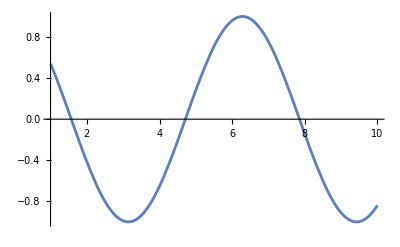

```mathematica
Plot[Cos[x α^3]/.{μ->1,ω-> 0.9,α->1},{x,1,10}]
```

```mathematica
FullSimplify[Real[Exp[-I ω t]],ω∈Reals&&t∈Reals]
```

Real[ⅇ^(-ⅈ t ω)]

```mathematica
tt=y[xt]/.DSolve[{D[y[xt],{xt,2}]==S0 (xt)^4 Exp[-xt]+β y[xt]+β2 y[xt]/xt,y[1000]==10^-50},y[xt],xt]⟦1⟧;
```

```mathematica
Series[tt ,{S0,0,1}]
```

(ⅇ^(xt (√-β-√β)-xt √-β) xt (ⅇ^(1000 √β) Hypergeometric1F1[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 xt √β]-100000000000000000000000000000000000000000000000000000 C[1] Hypergeometric1F1[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 xt √β] HypergeometricU[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2000 √β]+100000000000000000000000000000000000000000000000000000 C[1] Hypergeometric1F1[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2000 √β] HypergeometricU[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 xt √β]))/(100000000000000000000000000000000000000000000000000000 Hypergeometric1F1[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2000 √β])-1/(2 √β+β2)2 (ⅇ^(xt (√-β-√β)-xt √-β) xt (HypergeometricU[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 xt √β] ∫_1000^xt ((ⅇ^(-K[1]+(√-β-√β) K[1]-√-β K[1]+2 √β K[1]) Hypergeometric1F1[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 √β K[1]] K[1]^3)/(Hypergeometric1F1[2+β2/(2 √β),3,2 √β K[1]] HypergeometricU[1+β2/(2 √β),2,2 √β K[1]]+2 Hypergeometric1F1[1+β2/(2 √β),2,2 √β K[1]] HypergeometricU[2+β2/(2 √β),3,2 √β K[1]]))ⅆK[1]-Hypergeometric1F1[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 xt √β] ∫_1000^xt ((ⅇ^(-K[2]+(√-β-√β) K[2]-√-β K[2]+2 √β K[2]) HypergeometricU[1+(-4 √-β-2 (-2 √-β-β2))/(4 √β),2,2 √β K[2]] K[2]^3)/(Hypergeometric1F1[2+β2/(2 √β),3,2 √β K[2]] HypergeometricU[1+β2/(2 √β),2,2 √β K[2]]+2 Hypergeometric1F1[1+β2/(2 √β),2,2 √β K[2]] HypergeometricU[2+β2/(2 √β),3,2 √β K[2]]))ⅆK[2])) S0+O[S0]^2

```mathematica
Series[1/(-1+β)^5 ⅇ^-xt S0 (120+96 xt+36 xt^2+8 xt^3+xt^4+240 β-60 xt^2 β-24 xt^3 β-4 xt^4 β+24 β^2-96 xt β^2+12 xt^2 β^2+24 xt^3 β^2+6 xt^4 β^2+12 xt^2 β^3-8 xt^3 β^3-4 xt^4 β^3+xt^4 β^4)+ⅇ^(-xt √β) C[2] ,{S0,Infinity,1},{xt,rp,0}]
```

(1/(-1+β)^5 ⅇ^-rp (120+96 rp+36 rp^2+8 rp^3+rp^4+240 β-60 rp^2 β-24 rp^3 β-4 rp^4 β+24 β^2-96 rp β^2+12 rp^2 β^2+24 rp^3 β^2+6 rp^4 β^2+12 rp^2 β^3-8 rp^3 β^3-4 rp^4 β^3+rp^4 β^4)+O[xt-rp]^1) S0+(ⅇ^(-rp √β) C[2]+O[xt-rp]^1)+O[1/S0]^2

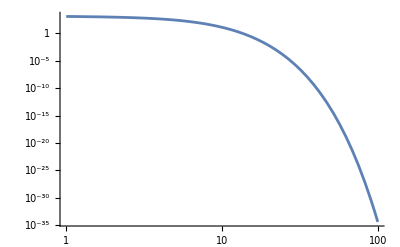

```mathematica
LogLogPlot[ⅇ^-x S0 (-120-96 x-36 x^2-8 x^3-x^4)/.{S0->-11},{x,1,100}]
```

```mathematica
1/α^(3/2)(α^(3/2)α^(3/2))^3 1/α^3
```

α^(9/2)

```mathematica
FullSimplify[Series[r √(1-(1-α^2/2)),{α,0,2}],α>0]
```

(r α)/(√2)+O[α]^3

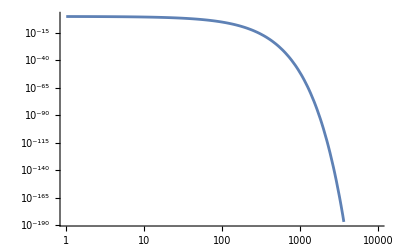

```mathematica
LogLogPlot[Exp[-r α/(√2)]/.{α->0.083 2},{r,1,10000}]
```